# DNA Melting Temperature Analysis Tool

Jefferson E. Bates & B. Lauren G. Woods
Fall 2024

In this notebook, you will read in your data from a simplified CSV file and process it in order to determine the melting temperatures and errors of the melting temperatures for different concentrations of dsDNA. This data will then be used in a second step by you to determine the enthalpy and entropy of the reaction (not done in this notebook).

BEFORE YOU START: 
Format your data! In order to use this tool, your data must be in CSV format with the temperatures in the first column, and the absorbance for each trial in subsequent columns. You do not need to include the data for the blank, just the samples that contained a finite concentration of dsDNA.

Instructions: (TODO : update numbering and code blocks)
1. Change Code Block I.1 by specifying the correct number of well-plates used in the experiment. This should generally be equal to the number of distinct concentrations of dsDNA.
2. Change Code Block I.A.1 by specifying the location of your “.csv” data file. Further instructions can be found inside the code block.
3. Change Code Block I.B.2 by modifying columnlist to reflect the numbers of the columns your group used on  the micro-plate. DO NOT SPECIFY MORE COLUMNS THAN WERE USED IN LAB!  ONLY NEED THIS STEP IF WE KEEP COLUMN SELECTION.
4. Change Code Block I.B.4 to specify the first 2 temperatures of the chillers used to cool the well-plates. You must put the lowest temperature first. This is only needed if the temperatures are not present in the imported CSV file.
5. Execute the notebook using “Evaluation --> Execute Notebook” and check the output in Code Block I.B.11 and Code Block II.A.3.
6. Check Code Block I.B.3  to make sure that the red framed output corresponds to the number of trials you decided to keep and that the “sanity check” is true. 
Note: Double clicking any of the “folded” sections on the right should expand them, or you can click on the arrow to the left of the section name.

## 0. Helper Functions

YOU SHOULD NOT BE MODIFYING ANYTHING IN THIS SECTION!

#### Code Block H.1 : Ideal Gas Constant (J/mol K)

Ultimately you will need the ideal gas constant, R, so it is provided here in certain units. Keep these in mind when analyzing the results!

```mathematica
RJoules = 8.314510(*J / K mol*);
```

#### Code Block H.2 : sigmoidfit Helper Function

The function below is designed to help you fit your experimental data to a sigmoidal curve.

```mathematica
sigmoidfit[data_]:=Block[{x,nlm,c0,c1,c2,c3,model},
(*** Assumes data is organized in columns: Temperature, Absorbance
Input : list of experimental results for temperatures and absorbance values;
 Output : A NonlinearModelFit object
***)
model = (c0 + c1*Tanh[(x-c2)/c3]);
nlm = NonlinearModelFit[data,model,{{c0,0.85},c1,{c2,35},c3},x]
]
```

#### Code Block H.3 : molar absorptivity of DNA

```mathematica
ϵDNA = 135092.6;
```

## I. Import and Average Melting Curve Data for Different Concentrations

#### Code Block I.1 : Specify the number of plates (concentrations) & number of temperature points

Set the number of DNA plates to be used in the instrument ; nplates = number of concentrations.
So if you have 6 concentrations, nplates =  6.

```mathematica
nplates = 6 ;
```

### A. Specify the input file to process

In order to process all of your data as efficiently as possible, please place the “txt” file generated by the instrument in the same directory where you will save this Mathematica notebook. In the Code Block I.A.1 below, you will insert the file path to your text file, so that Mathematica can extract all of the pertinent data for analysis.

The simplest way to insert the correct file path is the following:
	1. click on “Insert” above 
	2. choose “File Path...” 
After you choose “File Path”, you should be provided with a file browser where you then locate your files in a more familiar fashion.

#### Code Block I.A.1 : Specify CSV file to Import

It is HIGHLY recommended that you try to run this notebook on the provided sample data BEFORE attempting your data analysis. This way you know if the files are being uploaded correctly.

```mathematica
filename="/home/jebbate/Downloads/dna_data_col1_2.csv"
```

/home/jebbate/Downloads/dna_data_col1_2.csv

### B. Import and Process the Data

#### Code Block I.B.1 : Import the CSV file and extract the data for each concentration

Using some string parsing in Mathematica, the data for different concentrations can be extracted in order to facilitate the nonlinear fitting below. We will store these results in the variable procdata.

```mathematica
allcsvdata = Import[filename,"CSV"];
ntemps=Length[allcsvdata]/nplates;
procdata=Block[{alldata,tmpdata},
alldata={};
For[ii=1,ii≤ Length[allcsvdata],ii+=ntemps,
tmpdata=allcsvdata[[ii;;ii+ntemps-1]];
AppendTo[alldata,tmpdata];
];
alldata
];
Length[procdata]
Do[Print[Length[procdata[[ii]]]], {ii, %}]
```

6

10

10

10

«3 more identical outputs»

#### Code Block I.B.2 : Plot data for first trials

With the data Imported, here is a Plot to make sure that everything worked properly. This plot should reflect the first trial of your experimental data.

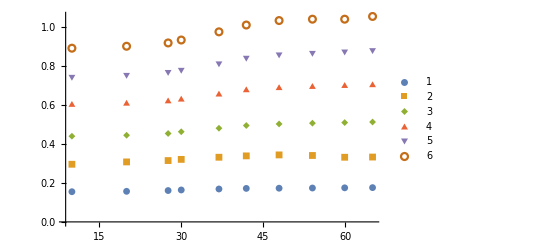

```mathematica
ListPlot[Table[procdata[[ii]][[All,{1, 2}]], 
   {ii, 1, Length[procdata]}], PlotMarkers -> 
   {Automatic, Small}, PlotLegends -> 
   {Table[ii, {ii, 1, Length[procdata]}]}, PlotRange -> All]
```

Now that your data has been imported properly, we can normalize each trial and then average the trials together.

#### Code Block I.B.3 : Normalize trial data for each concentration & extract concentrations

The below code block uses some ADVANCED Mathematica techniques to handle lists. A full discussion of this information is beyond the scope of this notebook. The OUTPUT of this Code Block is a new variable, newdata, that is NORMALIZED based upon the final temperature point. The concentrations of the DNA are also caclulated using Beer’s law and an assumed molar-absorptivity given in Code Block H.3 above.

```mathematica
xvals = (#1[[All,1]] & ) /@ procdata; 
yvals = (Transpose[Drop[Transpose[#1], 1]] & ) /@ procdata; 
(* compute the concentrations here before normalization ; put in μM units *)
concentrations=Map[Mean[#1[[1]]]&,yvals]/ϵDNA * 10^6;
normalizedy = (Transpose[(#1/#1[[-1]] & ) /@ Transpose[#1]] & ) /@ yvals; 
Transpose[{xvals, normalizedy}]; 
newdata = ((Flatten[#1] & ) /@ Transpose[#1] & ) /@ %; 
Length[newdata]
```

6

#### Code Block I.B.4 : Plot normalized data

Below is a plot of the First Trial, as before, but now the value at 60 C is set equal to 1 identically.

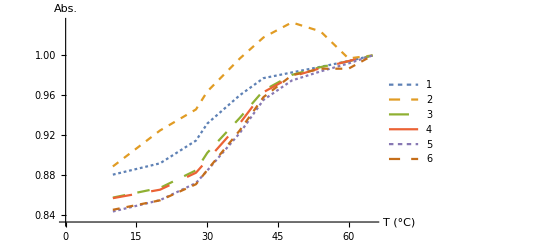

```mathematica
ListPlot[Table[newdata[[ii]][[All,{1, 2}]], 
   {ii, 1, Length[procdata]}], PlotLegends -> 
   {Table[ii, {ii, 1, Length[procdata]}]},  
  Joined -> True, PlotStyle -> {Dashing[Tiny], 
    Dashing[Small], Dashing[Medium], Dashing[Large]}, 
  AxesLabel -> {"T (°C)", "Abs."}]
```

#### Code Block I.B.5 : Average trial data for each concentration

With normalized absorbance data in hand, now we can now take an average over the trials to get one data set PER concentration. The length of avgdata should correspond to the number of concentrations (nplates)

```mathematica
Map[Map[Mean[#]&,Transpose[Drop[Transpose[#],1]]]&,newdata];
avgdata=MapThread[Transpose[{#1,#2}]&,{xvals,%}];
Length[%]
```

6

Below in Code Block I.B.6, you will find a plot of the NORMALIZED, AVERAGE melting curves from your trials. If you compare the Plots from Code Block I.B.4 and 1.B.6, the curves in 1.B.6 will *hopefully* be smoother due to the averaging.

#### Code Block I.B.6 : Plot of the average melting curve for each concentration

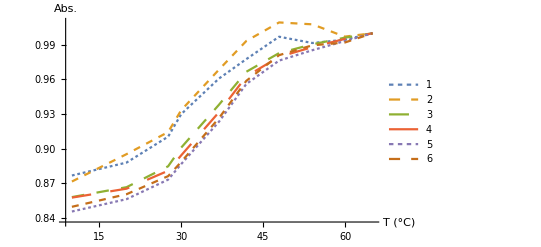

```mathematica
ListPlot[Table[avgdata[[ii]][[All,{1,2}]],{ii,1,Length[a1]}],PlotLegends->List[Table[ii,{ii,1,Length[procdata]}]],PlotRange->All,Joined->True,PlotStyle->{Dashing[Tiny],Dashing[Small],Dashing[Medium],Dashing[Large]},AxesLabel->{"T (°C)","Abs."}]
```

Your plot should have the same general shape in Code Block 1.B.6 as the example data (SEE BELOW).   If the plots are not similar, then there were issues with importing your data.  If the plots are similar, you are ready to proceed to Section II!
-Graphics-
Figure 1.1. Example of what your plot should look like in Code Block I.B.6. 
NOTE: The plot immediately above is NOT your experimental data, but that from the J. Chem. Ed. reference paper.

## II. Determination of Melting Temperature for all Concentrations

### A. Fit Experimental Data Based on a Model Sigmoid Function

In this section, we will use the power of Mathematica to perform some Nonlinear curve fitting of your absorbance data. This procedure is nonlinear because the underlying function is not a “linear function of x,” i.e. it depends on x in a non-linear fashion such as x^2 or Tanh[x]. In general, the melting curve has a sigmoidal shape and we can use 3 parameters to describe it:
f(x,c1,c2,c3) = c0 + c1 Tanh((x-c2)/c3)
where c0 describes the midpoint value of the curve, c1 is related to the “steepness” of the curve, c2 characterizes the x value at the midpoint (which will be the melting temperature in this experiment), and c3 provides some additional flexibility with the curvature. In Code Block II.A.1 is an example plot for a midpoint of 0.9 absorbance, a melting temperature of 38.5 °C, and some reasonably chosen values for c1 and c3. The vertical line indicates the T_m value, which in this case is equal to c2, 38.5 °C.

#### Code Block II.A.1 : Example Plot of the Sigmoid Model Function

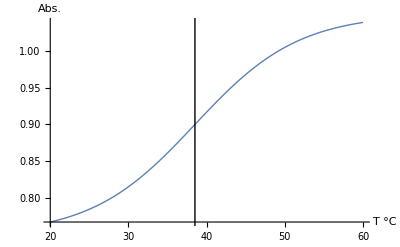

```mathematica
model=c0+c1 Tanh[(x-c2)/c3];
Plot[model/.{c0->0.9,c1->0.15,c2->38.5,c3->13.3},{x,20,60},PlotRange->All,AxesLabel->{"T °C", "Abs."},PlotStyle->{Automatic,Thick},
Epilog->{Line[{{38.5,0},{38.5,1.05}}]}]
```

To help us fit the data, we will need a new function that takes the temperature and absorbance data for a given concentration and produces a fit of the data that we can use to determine T_m. The sigmoidfit function below takes a list of {x,y} pairs, {{x1,y1}, {x2,y2}, {x3,y3}...}, and outputs an object that contains A LOT of useful information. Execute Code Block II.A.2 below to store the sigmoidfit function into the Mathematica kernel. There should be no output from this Code Block.

Using the sigmoidfit helper function from Code Block H.2, let’s test it out on the LOWEST value of concentration from your data in Code Block I.B.1. The lines of code below for lineq and linfiterr can be used to extract the fit parameters (of which you ONLY care about c2), respectively.  A plot is is given at the end  of the output that should overlay the data and the fit curve. Double check that these visually agree and that the assignment of T_m was done properly. The R^2 value also reflects the accuracy of the fit, so make sure it is close to 1; if it is much less than 0.9, the fit is likely poor.

#### Code Block II.A.2 : Example application of sigmoidfit helper function

The code below extracts the first element of the averaged data, performs a nonlinear fit using sigmoidfit, and then outputs the fit parameters, their errors, and a plot of the fit + data.

FittedModel[0.935982+0.0617445 Tanh[0.0886528 (-31.8498+x)]]

0.999989

{c0→0.935982,c1→0.0617445,c2→31.8498,c3→11.28}

{0.0022852,0.00286628,0.717179,1.30872}

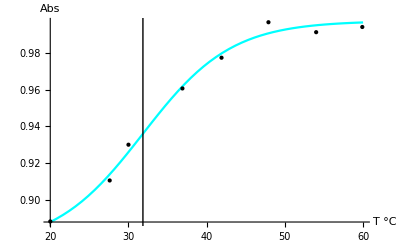

```mathematica
c1data= avgdata[[1]];
nlm0=sigmoidfit[c1data]
rsqlin = nlm0["RSquared"]
lineq = nlm0["BestFitParameters"]
linfiterr = nlm0["ParameterErrors"]
Plot[nlm0["BestFit"],{x,20,60},PlotStyle->Cyan,Epilog->{Point[c1data],Line[{{c2/.lineq,0},{c2/.lineq,1}}]},AxesLabel->{"T °C","Abs"}]
```

If the fit looks to be working properly, we can now apply it to all of your concentrations in one go using “Map”, a Mathematica function that applies sigmoidfit to each set of data in the avgdata list. Then we can extract the T_m values and errors from the fit parameters. This procedure is done for you in Code Block II.A.4.

#### Code Block II.A.3 : Fit all of the experimental data and extract melting temperatures

Using /@ (which is equal to Map[]), we can apply sigmoidfit to all of the data stored inside avgdata. Then we can extract the fit parameters and the fit errors.  Below are the values for T_m (in Celsius) in the order of the files uploaded.

```mathematica
sigmoidfits = sigmoidfit/@avgdata;
tmvalues = Map[{c2/.#1["BestFitParameters"],#1["ParameterErrors"][[3]]}&,sigmoidfits];
```

Now that everything is calculated, we can put the results together and display them in a table that you can use in a second step to calculate the fit of the data.  Please use the values in the table below to compute the necessary inputs for the van’t Hoff equation fit using the Ordinary Least Squares Fit notebook available on the ASULearn page. You will need to use rigorous error analysis in order to correctly propagate the error in the melting temperature.

```mathematica
Print["Please use the following data for your data analysis : "]
MapThread[{N[#1],#2[[1]],#2[[2]]}&, {concentrations, tmvalues}];
Insert[%,{"Conc (μM)", "Tm (deg C)", "Tm Err (deg C)"},1];
TableForm[%]
```

Please use the following data for your data analysis :

Conc (μM) | Tm (deg C) | Tm Err (deg C)
1.15846 | 31.8498 | 0.717179
2.20219 | 31.2053 | 1.06575
3.33475 | 34.9515 | 0.363099
4.50432 | 35.9904 | 0.412188
5.55545 | 36.2454 | 0.447899
6.63249 | 36.1804 | 0.386615